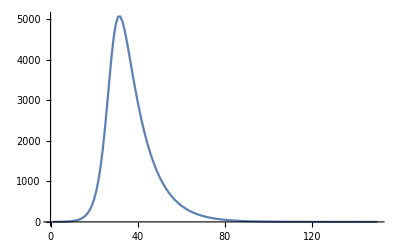

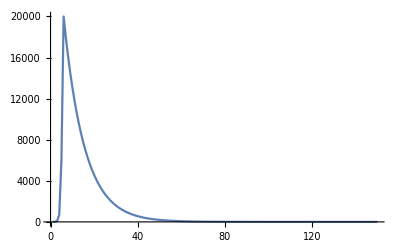

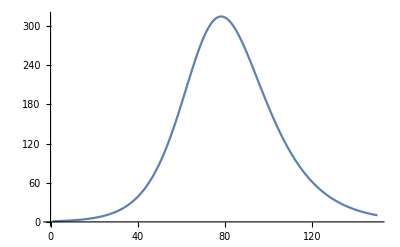

```mathematica
Clear["Global`*"];

EulerMethod[s0_, beta_,alpha_, range_]:=(
patchesCount=Length[s0];
rangeStart = range[[1]];
rangeEnd = range[[2]];
steps = Table[x, {x, rangeStart, rangeEnd}];

For[i=1,i<=patchesCount,i++,
idata[i][1]=1;
sdata[i][1]=s0[[i]];

(*Print["sdata[",i,"][1] = ",sdata[i][1]];
Print["idata[",i,"][1] = ",idata[i][1]];*)
];

For[j=1,j<Length[steps],j++,
x=steps[[j]];
nextX = steps[[j+1]];
lambda=ConstantArray[0,patchesCount];

For[i = 1, i<=patchesCount,i++,
For[k = 1, k<=patchesCount,k++,
lambda[[i]]+=beta[[i]][[k]] idata[k][x];
];
];

For[i=1, i<=patchesCount,i++,
	currentN=n[[i]];
	sdata[i][nextX]=sdata[i][x]+d*currentN-d*sdata[i][x]-lambda[[i]]sdata[i][x];
	idata[i][nextX]=idata[i][x]+lambda[[i]]sdata[i][x]-d idata[i][x]-alpha idata[i][x];
	(*Print["sdata[",i,"][",nextX,"] = ",sdata[i][nextX]];
	Print["idata[",i,"][",nextX,"] = ",idata[i][nextX]];*)
	sdata[i][nextX]=Max[0, Min[n[[i]], sdata[i][nextX]]];
	idata[i][nextX]=Max[0, Min[n[[i]], idata[i][nextX]]];
];
];

results=ConstantArray[{},patchesCount];

For[i=1,i≤patchesCount,i++,
results[[i]]=Table[{j, idata[i][j]}, {j, rangeStart, rangeEnd}];
];

results
);

range={1, 150};
beta = {{0.00005,0,0},
	  {0,0.0004 ,0},
	  {0,0,0.0001}};
alpha = 0.1;

d=0;
n={10000,20000,2000};

(* Remove the 1 that is patient zero *)
s0=Map[Function[x,x-1],n];

results=EulerMethod[s0, beta,alpha,range];

For[i=1,i≤Length[results],i++,
Print[ListPlot[results[[i]],PlotRange->All, Joined->True]];
]
```